## Import data files and create interpolation objects

Form factors  span the range q = 1 to 2000 keV and E = 1 eV to 2 keV. 
q is the momentum transfer [in keV] and E is the electron kinetic energy [in keV].
Data is optimised for q = 1 to 500 keV and E = 1 eV to 1 keV. 
Interpolation outside this range is not accurate.

```mathematica
SetDirectory[NotebookDirectory[]];

(*core*)
LC4H101a1grid=Import["C4H10_1a1_grid.dat"];
LC4H101e1grid=Import["C4H10_1e1_grid.dat"];
LC4H101e2grid=Import["C4H10_1e2_grid.dat"];
LC4H102a1grid=Import["C4H10_2a1_grid.dat"];

LC4H103a1grid=Import["C4H10_3a1_grid.dat"];
LC4H102e1grid=Import["C4H10_2e1_grid.dat"];
LC4H102e2grid=Import["C4H10_2e2_grid.dat"];
LC4H104a1grid=Import["C4H10_4a1_grid.dat"];

(*inner valence*)
LC4H105a1grid=Import["C4H10_5a1_grid.dat"];
LC4H103e1grid=Import["C4H10_3e1_grid.dat"];
LC4H103e2grid=Import["C4H10_3e2_grid.dat"];

(*outer valence*)
LC4H104e1grid=Import["C4H10_4e1_grid.dat"];
LC4H104e2grid=Import["C4H10_4e2_grid.dat"];
LC4H1051a2grid=Import["C4H10_1a2_grid.dat"];
LC4H1051a2grid=Import["C4H10_1a2_grid.dat"];
LC4H105e1grid=Import["C4H10_5e1_grid.dat"];
LC4H105e2grid=Import["C4H10_5e2_grid.dat"];
LC4H106a1grid=Import["C4H10_6a1_grid.dat"];
ResetDirectory[];

(*core*)
fC4H101a1=Interpolation[LC4H101a1grid,InterpolationOrder->1]
fC4H101e1=Interpolation[LC4H101e1grid,InterpolationOrder->1]
fC4H101e2=Interpolation[LC4H101e2grid,InterpolationOrder->1]
fC4H102a1=Interpolation[LC4H102a1grid,InterpolationOrder->1]

(*inner valence*)
fC4H103a1=Interpolation[LC4H103a1grid,InterpolationOrder->1]
fC4H102e1=Interpolation[LC4H102e1grid,InterpolationOrder->1]
fC4H102e2=Interpolation[LC4H102e2grid,InterpolationOrder->1]
fC4H104a1=Interpolation[LC4H104a1grid,InterpolationOrder->1]

(*outer valence*)
fC4H105a1=Interpolation[LC4H105a1grid,InterpolationOrder->1]
fC4H103e1=Interpolation[LC4H103e1grid,InterpolationOrder->1]
fC4H103e2=Interpolation[LC4H103e2grid,InterpolationOrder->1]
fC4H104e1=Interpolation[LC4H104e1grid,InterpolationOrder->1]
fC4H104e2=Interpolation[LC4H104e2grid,InterpolationOrder->1]
fC4H101a2=Interpolation[LC4H1051a2grid,InterpolationOrder->1]
fC4H105e1=Interpolation[LC4H105e1grid,InterpolationOrder->1]
fC4H105e2=Interpolation[LC4H105e2grid,InterpolationOrder->1]
fC4H106a1=Interpolation[LC4H106a1grid,InterpolationOrder->1]
```

InterpolatingFunction[…]

InterpolatingFunction[…]

InterpolatingFunction[…]

«14 more identical outputs»

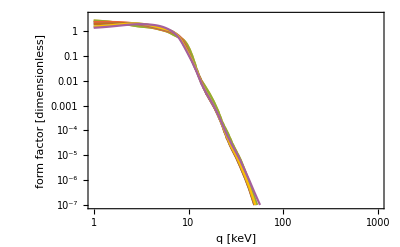

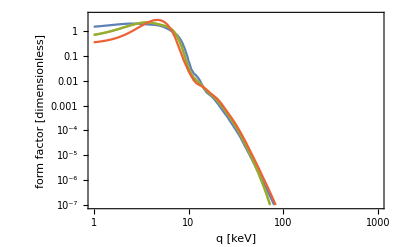

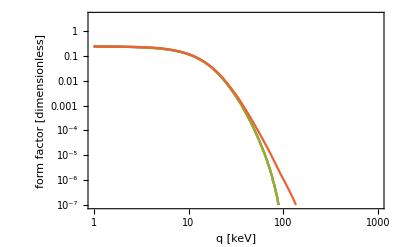

```mathematica
EtestkeV=0.025;

LogLogPlot[{fC4H106a1[q,EtestkeV],fC4H105e2[q,EtestkeV],fC4H105e1[q,EtestkeV],fC4H101a2[q,EtestkeV],fC4H104e2[q,EtestkeV],fC4H104e1[q,EtestkeV],fC4H103e2[q,EtestkeV],fC4H103e1[q,EtestkeV],fC4H105a1[q,EtestkeV]},{q,1,200},PlotRange->{{1,1000},{10^-7,4}},Frame->True,FrameLabel->{"q [keV]","form factor [dimensionless]"}]

LogLogPlot[{fC4H104a1[q,EtestkeV],fC4H102e2[q,EtestkeV],fC4H102e1[q,EtestkeV],fC4H103a1[q,EtestkeV]},{q,1,200},PlotRange->{{1,1000},{10^-7,4}},Frame->True,FrameLabel->{"q [keV]","form factor [dimensionless]"}]

LogLogPlot[{fC4H102a1[q,EtestkeV],fC4H101e2[q,EtestkeV],fC4H101e1[q,EtestkeV],fC4H101a1[q,EtestkeV]},{q,1,200},PlotRange->{{1,1000},{10^-7,4}},Frame->True,FrameLabel->{"q [keV]","form factor [dimensionless]"}]
```

### check that the e orbitals are degenerate after rotational averaging - a check on numerical results

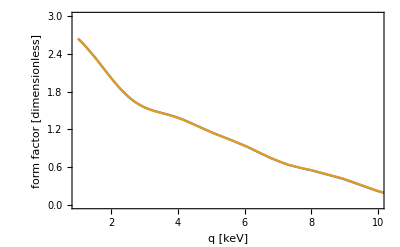

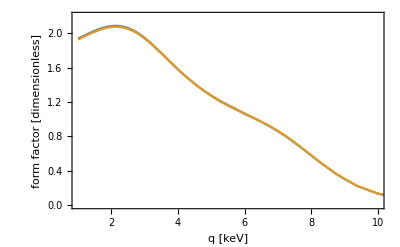

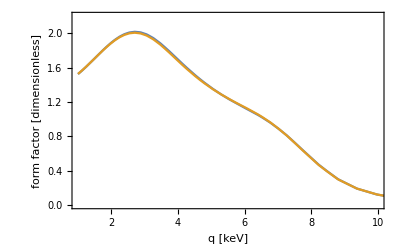

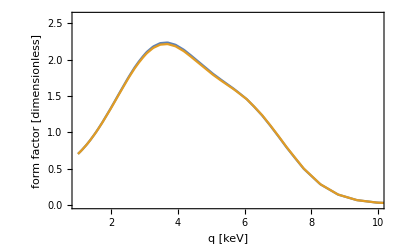

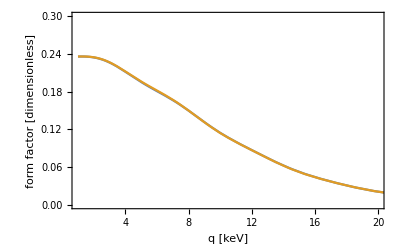

```mathematica
EtestkeV=0.025;

Plot[{fC4H105e1[q,EtestkeV],fC4H105e2[q,EtestkeV]},{q,1,100},PlotRange->{{1,10},{10^-7,3}},Frame->True,FrameLabel->{"q [keV]","form factor [dimensionless]"}]

Plot[{fC4H104e1[q,EtestkeV],fC4H104e2[q,EtestkeV]},{q,1,100},PlotRange->{{1,10},{10^-7,2.2}},Frame->True,FrameLabel->{"q [keV]","form factor [dimensionless]"}]

Plot[{fC4H103e1[q,EtestkeV],fC4H103e2[q,EtestkeV]},{q,1,100},PlotRange->{{1,10},{10^-7,2.2}},Frame->True,FrameLabel->{"q [keV]","form factor [dimensionless]"}]

Plot[{fC4H102e1[q,EtestkeV],fC4H102e2[q,EtestkeV]},{q,1,100},PlotRange->{{1,10},{10^-7,2.6}},Frame->True,FrameLabel->{"q [keV]","form factor [dimensionless]"}]

Plot[{fC4H101e1[q,EtestkeV],fC4H101e2[q,EtestkeV]},{q,1,100},PlotRange->{{1,20},{0,.3}},Frame->True,FrameLabel->{"q [keV]","form factor [dimensionless]"}]
```